# Optical Bloch equations with phenomenological decoherence

```mathematica
SetOptions[#,PlotRange->All,Axes->False,Frame->True,PlotStyle->{Thick,Red},LabelStyle->{FontFamily->"Helvetica",FontSize->16}]&/@{Plot};
```

```mathematica
H=ℏ/2({{-Δ, -Ω}, {-Conjugate[Ω], Δ}});
R=({{Subscript[ρ, ee], Subscript[ρ, eg]}, {Subscript[ρ, ge], Subscript[ρ, gg]}});
asm={ℏ>0,Δ∈Reals,0<=Subscript[ρ, ee]≤1,0≤Subscript[ρ, gg]≤1};
```

```mathematica
RHS=FullSimplify[-I/ℏ(H.R-R.H),Assumptions->asm];
%//TraditionalForm
```

(-1/2 ⅈ (Conjugate[Ω] ρ_eg-Ω ρ_ge) | 1/2 ⅈ (-Ω ρ_ee+2 Δ ρ_eg+Ω ρ_gg)
1/2 ⅈ (Conjugate[Ω] (ρ_ee-ρ_gg)-2 Δ ρ_ge) | 1/2 ⅈ (Conjugate[Ω] ρ_eg-Ω ρ_ge))

```mathematica
rhovec={Subscript[ρ, ee],Subscript[ρ, eg],Subscript[ρ, ge],Subscript[ρ, gg]};
vec={
RHS[[1,1]]-Subscript[Γ, p] (Subscript[ρ, ee]-Subsuperscript[ρ,ee,ss]),
RHS[[1,2]]-Subscript[Γ, c] Subscript[ρ, eg],
RHS[[2,1]]-Subscript[Γ, c] Subscript[ρ, ge],
RHS[[2,2]]-Subscript[Γ, p](Subscript[ρ, gg]-Subsuperscript[ρ,gg,ss])};
M=Transpose[Coefficient[vec,#]&/@rhovec];
%//TraditionalForm
m=Transpose[{Total[Coefficient[vec,#]&/@{Subsuperscript[ρ,gg,ss],Subsuperscript[ρ,ee,ss]}]}];
%//TraditionalForm
```

(-Γ_p | -(ⅈ Conjugate[Ω])/2 | (ⅈ Ω)/2 | 0
-(ⅈ Ω)/2 | -Γ_c+ⅈ Δ | 0 | (ⅈ Ω)/2
(ⅈ Conjugate[Ω])/2 | 0 | -Γ_c-ⅈ Δ | -(ⅈ Conjugate[Ω])/2
0 | (ⅈ Conjugate[Ω])/2 | -(ⅈ Ω)/2 | -Γ_p)

(Γ_p
0
0
Γ_p)

```mathematica
Q=Simplify[M/.{Δ->0,Subscript[Γ, p]->0},Assumptions->{Ω>0}];
%//TraditionalForm
```

(0 | -(ⅈ Ω)/2 | (ⅈ Ω)/2 | 0
-(ⅈ Ω)/2 | -Γ_c | 0 | (ⅈ Ω)/2
(ⅈ Ω)/2 | 0 | -Γ_c | -(ⅈ Ω)/2
0 | (ⅈ Ω)/2 | -(ⅈ Ω)/2 | 0)

```mathematica
Mexp=FullSimplify[MatrixExp[-Q t],Assumptions->{Subscript[Γ, c]>0,Ω>0,t>0}];
%//TraditionalForm
```

(1/2 (-(Γ_c ⅇ^((t Γ_c)/2) sinh(1/2 t √(Γ_c^2-4 Ω^2)))/(√(Γ_c^2-4 Ω^2))+ⅇ^((t Γ_c)/2) cosh(1/2 t √(Γ_c^2-4 Ω^2))+1) | (ⅈ Ω ⅇ^((t Γ_c)/2) sinh(1/2 t √(Γ_c^2-4 Ω^2)))/(√(Γ_c^2-4 Ω^2)) | -(ⅈ Ω ⅇ^((t Γ_c)/2) sinh(1/2 t √(Γ_c^2-4 Ω^2)))/(√(Γ_c^2-4 Ω^2)) | 1/2 ((Γ_c ⅇ^((t Γ_c)/2) sinh(1/2 t √(Γ_c^2-4 Ω^2)))/(√(Γ_c^2-4 Ω^2))-ⅇ^((t Γ_c)/2) cosh(1/2 t √(Γ_c^2-4 Ω^2))+1)
(ⅈ Ω ⅇ^((t Γ_c)/2) sinh(1/2 t √(Γ_c^2-4 Ω^2)))/(√(Γ_c^2-4 Ω^2)) | (ⅇ^(1/2 t (Γ_c-√(Γ_c^2-4 Ω^2))) (√(Γ_c^2-4 Ω^2) (ⅇ^(t √(Γ_c^2-4 Ω^2))+2 ⅇ^(1/2 t (√(Γ_c^2-4 Ω^2)+Γ_c))+1)+Γ_c (ⅇ^(t √(Γ_c^2-4 Ω^2))-1)))/(4 √(Γ_c^2-4 Ω^2)) | -(ⅇ^(1/2 t (Γ_c-√(Γ_c^2-4 Ω^2))) (√(Γ_c^2-4 Ω^2) (ⅇ^(t √(Γ_c^2-4 Ω^2))-2 ⅇ^(1/2 t (√(Γ_c^2-4 Ω^2)+Γ_c))+1)+Γ_c (ⅇ^(t √(Γ_c^2-4 Ω^2))-1)))/(4 √(Γ_c^2-4 Ω^2)) | -(ⅈ Ω ⅇ^((t Γ_c)/2) sinh(1/2 t √(Γ_c^2-4 Ω^2)))/(√(Γ_c^2-4 Ω^2))
-(ⅈ Ω ⅇ^((t Γ_c)/2) sinh(1/2 t √(Γ_c^2-4 Ω^2)))/(√(Γ_c^2-4 Ω^2)) | -(ⅇ^(1/2 t (Γ_c-√(Γ_c^2-4 Ω^2))) (√(Γ_c^2-4 Ω^2) (ⅇ^(t √(Γ_c^2-4 Ω^2))-2 ⅇ^(1/2 t (√(Γ_c^2-4 Ω^2)+Γ_c))+1)+Γ_c (ⅇ^(t √(Γ_c^2-4 Ω^2))-1)))/(4 √(Γ_c^2-4 Ω^2)) | (ⅇ^(1/2 t (Γ_c-√(Γ_c^2-4 Ω^2))) (√(Γ_c^2-4 Ω^2) (ⅇ^(t √(Γ_c^2-4 Ω^2))+2 ⅇ^(1/2 t (√(Γ_c^2-4 Ω^2)+Γ_c))+1)+Γ_c (ⅇ^(t √(Γ_c^2-4 Ω^2))-1)))/(4 √(Γ_c^2-4 Ω^2)) | (ⅈ Ω ⅇ^((t Γ_c)/2) sinh(1/2 t √(Γ_c^2-4 Ω^2)))/(√(Γ_c^2-4 Ω^2))
1/2 ((Γ_c ⅇ^((t Γ_c)/2) sinh(1/2 t √(Γ_c^2-4 Ω^2)))/(√(Γ_c^2-4 Ω^2))-ⅇ^((t Γ_c)/2) cosh(1/2 t √(Γ_c^2-4 Ω^2))+1) | -(ⅈ Ω ⅇ^((t Γ_c)/2) sinh(1/2 t √(Γ_c^2-4 Ω^2)))/(√(Γ_c^2-4 Ω^2)) | (ⅈ Ω ⅇ^((t Γ_c)/2) sinh(1/2 t √(Γ_c^2-4 Ω^2)))/(√(Γ_c^2-4 Ω^2)) | 1/2 (-(Γ_c ⅇ^((t Γ_c)/2) sinh(1/2 t √(Γ_c^2-4 Ω^2)))/(√(Γ_c^2-4 Ω^2))+ⅇ^((t Γ_c)/2) cosh(1/2 t √(Γ_c^2-4 Ω^2))+1))

```mathematica
sol=(Mexp/.{t->-T}).(({{0}, {0}, {0}, {1}})+Integrate[Mexp.({{0}, {0}, {0}, {0}}),{t,0,T}]);
```

```mathematica
Pe=FullSimplify[sol[[1,1]],Assumptions->{T>.100,Subscript[Γ, c]>0,Ω>0}]
```

1/2 (1-ⅇ^(-(T Γ_c)/2) Cosh[1/2 T √(-4 Ω^2+Γ_c^2)]-(ⅇ^(-(T Γ_c)/2) Sinh[1/2 T √(-4 Ω^2+Γ_c^2)] Γ_c)/(√(-4 Ω^2+Γ_c^2)))

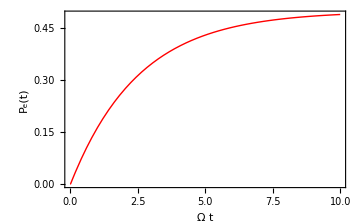

```mathematica
Plot[Pe/.{Subscript[Γ, c]->100,Ω->2Pi},{T,0,10},PlotRange->All,
FrameLabel->{"Ω t","P_e(t)"},ImageSize->Medium]
```